# Blatt 6

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->Round[MachinePrecision]]
```

## Import Data

```mathematica
rawData={155,184,5,135,134,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,130,8,20,216,7}
```

{155,184,5,135,134,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,130,8,20,216,7}

```mathematica
(*rawData={155,182,5,135,128,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,136,8,20,214,7}*)
```

```mathematica
rawData={155,184,5,135,131,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,133,8,20,216,7}
```

{155,184,5,135,131,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,133,8,20,216,7}

```mathematica
data=Partition[rawData,3]
```

{{155,184,5},{135,131,4},{120,99,4},{100,49,1},{90,53,3},{75,55,1},{65,70,4},{55,81,9},{40,133,8},{20,216,7}}

```mathematica
data//TeXForm//CopyToClipboard
```

## Processed Data

```mathematica
processedData={#[[1]],#[[2]]-#[[3]],N@Sqrt[#[[2]]+4 #[[3]]]}&/@data
```

{{155,179,14.2829},{135,127,12.1244},{120,95,10.7238},{100,48,7.28011},{90,50,8.06226},{75,54,7.68115},{65,66,9.27362},{55,72,10.8167},{40,125,12.8452},{20,209,15.6205}}

```mathematica
veryProcessedData={#[[1]], N@Cos[#[[1]] Degree],#[[2]],#[[3]]}&/@processedData
```

{{155,-0.906308,179,14.2829},{135,-0.707107,127,12.1244},{120,-0.5,95,10.7238},{100,-0.173648,48,7.28011},{90,0.,50,8.06226},{75,0.258819,54,7.68115},{65,0.422618,66,9.27362},{55,0.573576,72,10.8167},{40,0.766044,125,12.8452},{20,0.939693,209,15.6205}}

```mathematica
processedData//TeXForm//CopyToClipboard
```

## Legendre Fitting

```mathematica
LegendreP[0,x]
LegendreP[1,x]
LegendreP[2,x]
```

1

x

1/2 (-1+3 x^2)

```mathematica
f1[x_]:=1
f2[x_]:= x
f3[x_]:=1/2 (-1+3 x^2)
```

```mathematica
xdata=N@Cos[# Degree]&/@processedData[[All,1]]
ydata=processedData[[All,2]]
yerror=processedData[[All,3]]
```

{-0.906308,-0.707107,-0.5,-0.173648,0.,0.258819,0.422618,0.573576,0.766044,0.939693}

{179,127,95,48,50,54,66,72,125,209}

{14.2829,12.1244,10.7238,7.28011,8.06226,7.68115,9.27362,10.8167,12.8452,15.6205}

```mathematica
flst={f1,f2,f3}
```

{f1,f2,f3}

```mathematica
MatrixForm[Table[∑_(k=1)^Length[xdata] (flst⟦i⟧[xdata⟦k⟧] flst⟦j⟧[xdata⟦k⟧])/yerror⟦k⟧^2,{i,1,3},{j,1,3}]]
```

(0.101936 | 0.00582004 | -0.0159127
0.00582004 | 0.0233702 | -0.00040584
-0.0159127 | -0.00040584 | 0.0179312)

```mathematica
Δ=Det[Table[∑_(k=1)^Length[xdata] (flst⟦i⟧[xdata⟦k⟧] flst⟦j⟧[xdata⟦k⟧])/yerror⟦k⟧^2,{i,1,3},{j,1,3}]]
```

0.0000362501

```mathematica
sumf1f1=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f1[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf1f2=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf1f3=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf2f2=∑_(k=1)^Length[xdata] (f2[xdata⟦k⟧] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf2f3=∑_(k=1)^Length[xdata] (f2[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf3f3=∑_(k=1)^Length[xdata] (f3[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf1=∑_(k=1)^Length[xdata] (ydata[[k]] f1[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf2=∑_(k=1)^Length[xdata] (ydata[[k]] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf3=∑_(k=1)^Length[xdata] (ydata[[k]] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
```

```mathematica
Δ=Det[({{sumf1f1, sumf1f2, sumf1f3}, {sumf1f2, sumf2f2, sumf2f3}, {sumf1f3, sumf2f3, sumf3f3}})]
```

0.0000362501

```mathematica
a1=(1/Δ) Det[({{sumyf1, sumf1f2, sumf1f3}, {sumyf2, sumf2f2, sumf2f3}, {sumyf3, sumf2f3, sumf3f3}})]
a2=(1/Δ)Det[({{sumf1f1, sumyf1, sumf1f3}, {sumf1f2, sumyf2, sumf2f3}, {sumf1f3, sumyf3, sumf3f3}})]
a3=(1/Δ)Det[({{sumf1f1, sumf1f2, sumyf1}, {sumf1f2, sumf2f2, sumyf2}, {sumf1f3, sumf2f3, sumyf3}})]
```

97.4885

-8.56688

108.915

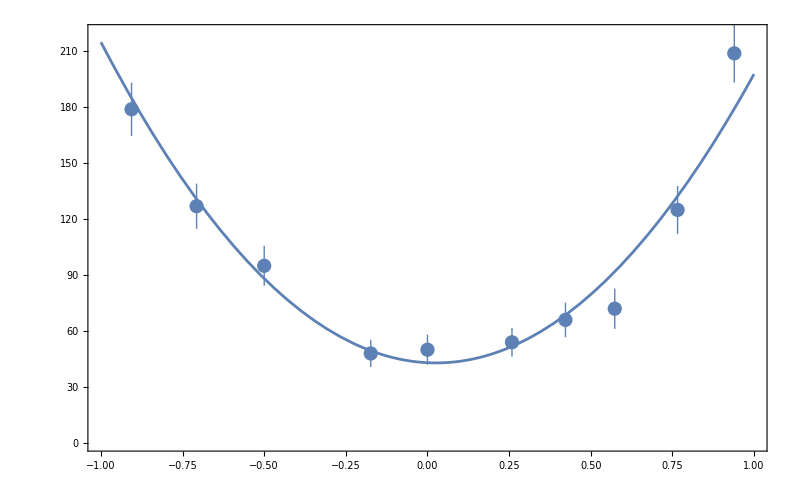

```mathematica
Show[ListPlot[{Cos[#[[1]]Degree],Around[#[[2]],#[[3]]]}&/@processedData], Plot[a1+a2 x+a3(-1+3 x^2)/2,{x,-1,1}],Frame->True,PlotRange->{{-1,1},{0,220}},Axes->False]
```

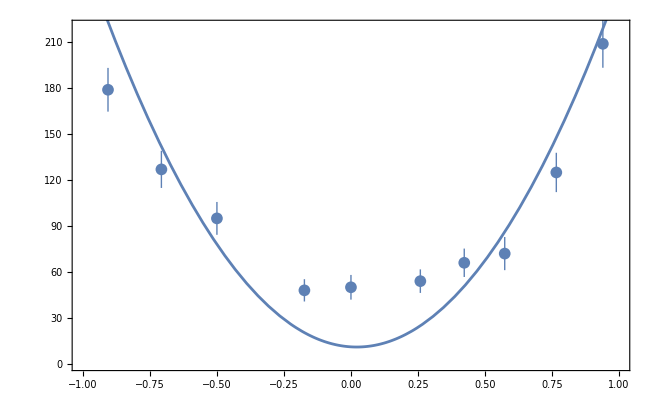

```mathematica
Show[ListPlot[{Cos[#[[1]]Degree],Around[#[[2]],#[[3]]]}&/@processedData], Plot[93.3-10.6 x+164.4(-1+3 x^2)/2,{x,-1,1}],Frame->True,PlotRange->{{-1,1},{0,220}},Axes->False]
```

```mathematica
FindFit[Transpose[{xdata, ydata}], a1f f1[x]+ a2f f2[x]+a3f f3[x],{a1f,a2f,a3f},x]
```

{a1f→97.4362,a2f→-4.59655,a3f→114.582}

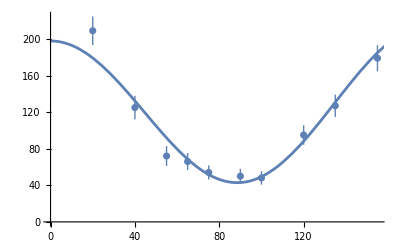

```mathematica
Show[ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@processedData], Plot[a1 f1[Cos[x Degree]]+a2 f2[Cos[x Degree]]+a3 f3[Cos[x Degree]],{x,0,200}]]
```

## Errors

```mathematica
({{f1[xdata⟦1⟧]/yerror⟦1⟧^2+ 2sumyf1, sumf1f2, sumf1f3}, {f2[xdata⟦1⟧]/yerror⟦1⟧^2+2sumyf2, sumf2f2, sumf2f3}, {f3[xdata⟦1⟧]/yerror⟦1⟧^2+2sumyf3, sumf2f3, sumf3f3}})//MatrixForm
```

(16.3141 | 0.00582004 | -0.0159127
0.641508 | 0.0233702 | -0.00040584
0.813885 | -0.00040584 | 0.0179312)

```mathematica
Table[Det[({{f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1, sumf1f2, sumf1f3}, {f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2, sumf2f2, sumf2f3}, {f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3, sumf2f3, sumf3f3}})],{k,1,Length[xdata]}]
```

{0.00707176,0.00707189,0.00707161,0.007073,0.00707154,0.00707211,0.00707133,0.00707102,0.00707088,0.00707053}

```mathematica
(1/Δ) Sqrt[Sum[(Det[({{f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1, sumf1f2, sumf1f3}, {f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2, sumf2f2, sumf2f3}, {f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3, sumf2f3, sumf3f3}})])^2 yerror[[k]]^2,{k,1,Length[xdata]}]]
(1/Δ) Sqrt[Sum[(Det[({{sumf1f1, f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1, sumf1f3}, {sumf1f2, f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2, sumf2f3}, {sumf1f3, f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3, sumf3f3}})])^2 yerror[[k]]^2,{k,1,Length[xdata]}]]
(1/Δ) Sqrt[Sum[(Det[({{sumf1f1, sumf1f2, f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1}, {sumf1f2, sumf2f2, f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2}, {sumf1f3, sumf2f3, f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3}})])^2 yerror[[k]]^2,{k,1,Length[xdata]}]]
```

6910.6

606.971

7720.55

```mathematica
(1/Δ) Sqrt[Sum[(Det[({{f1[xdata⟦k⟧]/yerror⟦k⟧^2, sumf1f2, sumf1f3}, {f2[xdata⟦k⟧]/yerror⟦k⟧^2, sumf2f2, sumf2f3}, {f3[xdata⟦k⟧]/yerror⟦k⟧^2, sumf2f3, sumf3f3}})]+Det[({{2sumyf1, sumf1f2, sumf1f3}, {2sumyf2, sumf2f2, sumf2f3}, {2sumyf3, sumf2f3, sumf3f3}})])^2yerror[[k]]^2,{k,1,Length[xdata]}]]
```

6910.6

```mathematica
yerror
```

{14.2829,12.1244,10.7238,7.28011,8.06226,7.68115,9.27362,10.8167,12.8452,15.6205}